```mathematica
RegionPlot3D[0<=z<=(((-1/8)*x^2)+(y^2/8)+3)&&0<=x^2+y^2<=16,{x,-5,5},{y,-5,5},{z,0,5},PlotPoints->90,Mesh->False,PlotStyle->Directive[Pink,Opacity[0.5]]]
```

-Graphics3D-

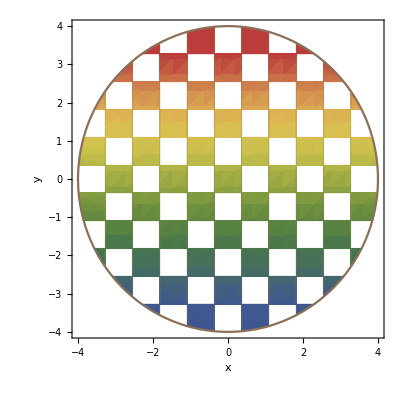

```mathematica
RegionPlot[x^2+y^2<16,{x,-4,4},{y,-4,4},Mesh->10,MeshShading->{{Automatic,None},{None,Automatic}}, ColorFunction->"DarkRainbow",AxesLabel->{x,y}]
```

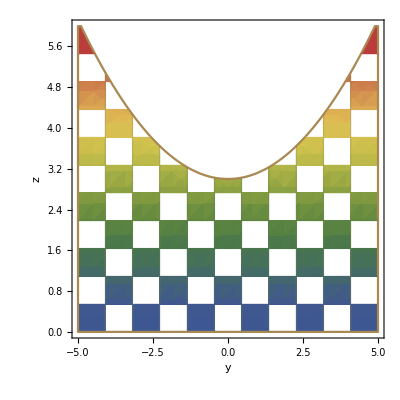

```mathematica
RegionPlot[z<(y^2/8)+3,{y,-5,5},{z,0,6},Mesh->10,MeshShading->{{Automatic,None},{None,Automatic}}, ColorFunction->"DarkRainbow",AxesLabel->{y,z}]
```

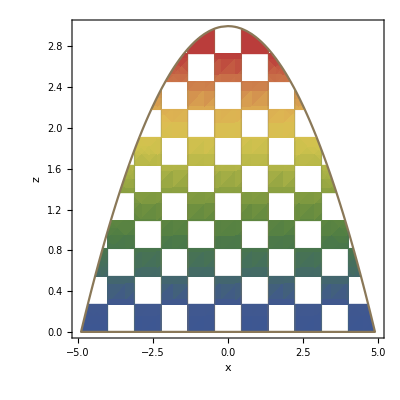

```mathematica
RegionPlot[z<-(x^2/8)+3,{x,-5,5},{z,0,3},Mesh->10,MeshShading->{{Automatic,None},{None,Automatic}}, ColorFunction->"DarkRainbow",AxesLabel->{x,z}]
```